```mathematica
(*Import the required packages*)
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]

(*Define the vector fitting function*)
VectorFitting[data_,poles_:10]:=Module[{z,w,p,x,y,f,g,rhs,coeffs},
(*Get the data points*)
x=Re[data];
y=Im[data];
(*Construct the Vandermonde matrix*)z=Exp[I x];
w=Flatten[Outer[Times,z,Range[poles]]];
p=LeastSquares[w.ConjugateTranspose[w],w.ConjugateTranspose[y]];
(*Construct the vector fitting function*)f=Sum[p[[i]]/(z-Exp[I x[[i]]]),{i,Length[x]}];
(*Calculate the residues and poles*)
g=Expand[Denominator[f]];
rhs=CoefficientList[g,z];
coeffs=CoefficientList[Numerator[f],z];
poles=z/. Solve[g==0,z];
(*Return the poles,residues,and the fitted function*){poles,rhs,coeffs,f}]
```

Dot::dotsh: Tensors {1,2,0.980067+0.198669 ⅈ,1.96013+0.397339 ⅈ,0.921061+0.389418 ⅈ,«19»+«18» ⅈ,0.825336+0.564642 ⅈ,1.65067+1.12928 ⅈ,0.696707+0.717356 ⅈ,1.39341+1.43471 ⅈ,«2»} and {0,0,0,0,0,0} have incompatible shapes.

LeastSquares::matrix: Argument 30.+0. ⅈ at position 1 is not a non-empty rectangular matrix.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Part::partw: Part 3 of LeastSquares[30.+0. ⅈ,{1,2,0.980067+0.198669 ⅈ,1.96013+0.397339 ⅈ,0.921061+0.389418 ⅈ,«1»,0.825336+«1»,1.65067+1.12928 ⅈ,0.696707+0.717356 ⅈ,1.39341+1.43471 ⅈ,«2»}.«1»] does not exist.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Part::partw: Part 4 of LeastSquares[30.+0. ⅈ,{1,2,0.980067+0.198669 ⅈ,1.96013+0.397339 ⅈ,0.921061+0.389418 ⅈ,«1»,0.825336+«1»,1.65067+1.12928 ⅈ,0.696707+0.717356 ⅈ,1.39341+1.43471 ⅈ,«2»}.«1»] does not exist.

Part::partw: Part 5 of LeastSquares[30.+0. ⅈ,{1,2,0.980067+0.198669 ⅈ,1.96013+0.397339 ⅈ,0.921061+0.389418 ⅈ,«1»,0.825336+«1»,1.65067+1.12928 ⅈ,0.696707+0.717356 ⅈ,1.39341+1.43471 ⅈ,«2»}.«1»] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

CoefficientList::ivar: 1 is not a valid variable.

General::stop: Further output of CoefficientList::ivar will be suppressed during this calculation.

Solve::ivar: 1 is not a valid variable.

ReplaceAll::reps: {Solve[{1,1,1,1,1,1}==0,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::setraw: Cannot assign to raw object 2.

Poles: 2

Residues: {CoefficientList[1,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}],CoefficientList[1,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}],CoefficientList[1,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}],CoefficientList[1,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}],CoefficientList[1,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}],CoefficientList[1,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}]}

Coefficients: {CoefficientList[ComplexInfinity,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}],CoefficientList[ComplexInfinity,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}],CoefficientList[ComplexInfinity,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}],CoefficientList[ComplexInfinity,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}],CoefficientList[ComplexInfinity,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}],CoefficientList[ComplexInfinity,{1,0.980067+0.198669 ⅈ,0.921061+0.389418 ⅈ,0.825336+0.564642 ⅈ,0.696707+0.717356 ⅈ,0.540302+0.841471 ⅈ}]}

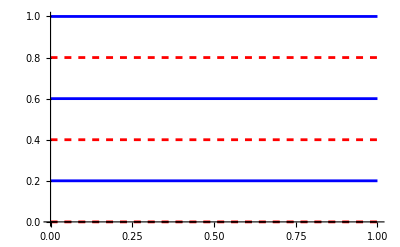

```mathematica
(*Example usage*)
data={0,0.2,0.4,0.6,0.8,1.0};
{poles,residues,coeffs,fit}=VectorFitting[data,2];

(*Print the results*)
Print["Poles: ",poles]
Print["Residues: ",residues]
Print["Coefficients: ",coeffs]
Plot[Evaluate[{fit,data}],{x,Min[data],Max[data]},PlotStyle->{Directive[Red,Dashed],Directive[Blue,PointSize[Large]]},Epilog->{Directive[Black,Dashed],Line[{{Min[data],0},{Max[data],0}}]}]
```